# functions

```mathematica
(* finds numerical value of λ parameter of triangle electrostatic center X(5626) *)
(* based on the Cartesian coordinates of triangle vertices *)
(* default value of Precision option is 12 decimal places *)
FindElectrostaticLambda[{{ax_,ay_},{bx_,by_},{cx_,cy_}},OptionsPattern[{Precision->12}]]:=
Module[{a,b,c,s,l,u,v,w,left,right,sol,p},
a=Norm[{cx,cy}-{bx,by}];b=Norm[{ax,ay}-{cx,cy}];c=Norm[{bx,by}-{ax,ay}];
u=a*Coth[(a*l)/(a+b+c)];v=b*Coth[(b*l)/(a+b+c)];w=c*Coth[(c*l)/(a+b+c)];
left=√((u^2-a^2)(a^2-(v-w)^2))+√((v^2-b^2)(b^2-(w-u)^2))+√((w^2-c^2)(c^2-(u-v)^2));
right=√(2(a^2 b^2+b^2 c^2+c^2 a^2)-(a^4+b^4+c^4));
sol=FindRoot[left==right,{l,1},AccuracyGoal->OptionValue[Precision],PrecisionGoal->OptionValue[Precision],WorkingPrecision->OptionValue[Precision],MaxIterations->10000];
Return[l/.sol];
]

(* computes a point on electrostatic line of the triangle *)
(* based on the λ parameter and Cartesian coordinates of triangle vertices *)
(* returns electrostatic center X(5626) if electrostatic center's λ is used *)
ElectrostaticLine[{{ax_,ay_},{bx_,by_},{cx_,cy_}},l_]:=
Module[{a,b,c,u,v,w,ka,kb,kc,dx,dy,nx,ny},
a=Norm[{cx,cy}-{bx,by}];b=Norm[{ax,ay}-{cx,cy}];c=Norm[{bx,by}-{ax,ay}];
u=a*Coth[(a*l)/(a+b+c)];v=b*Coth[(b*l)/(a+b+c)];w=c*Coth[(c*l)/(a+b+c)];
ka=ax^2+ay^2-v*w;kb=bx^2+by^2-w*u;kc=cx^2+cy^2-u*v;

dx=ka(by-cy)+kb(cy-ay)+kc(ay-by);
nx=2(ax(by-cy)+bx(cy-ay)+cx(ay-by));

dy=ka(bx-cx)+kb(cx-ax)+kc(ax-bx);
ny=2(ay(bx-cx)+by(cx-ax)+cy(ax-bx));

Return[{dx/nx,dy/ny}];
]

(* returns Cartesian coordinates of triangle electrostatic center X(5626) *)
(* triangle is defined with Cartesian coordinates of its vertices *)
(* default value of Precision option is 12 decimal places *)
FindElectrostaticCenter2D[{{ax_,ay_},{bx_,by_},{cx_,cy_}},OptionsPattern[{Precision->12}]]:=ElectrostaticLine[{{ax,ay},{bx,by},{cx,cy}},FindElectrostaticLambda[{{ax,ay},{bx,by},{cx,cy}},Precision->OptionValue[Precision]]]

(* 3D case *)
FindElectrostaticCenter3D[{{ax_,ay_,az_},{bx_,by_,bz_},{cx_,cy_,cz_}},OptionsPattern[{Precision->12}]]:=
Module[{vc,c,vt,vb,x0,vn,y0,ect,ecn,x,y,z},
vc={bx-ax,by-ay,bz-az};
c=Norm[vc];
vt=vc/c;

vb={cx-ax,cy-ay,cz-az};
x0=vb.vt;
vn=vb-x0*vt;
y0=Norm[vn];

{ect,ecn}=FindElectrostaticCenter2D[{{0,0},{c,0},{x0,y0}},Precision->OptionValue[Precision]];

vn=vn/y0;
{x,y,z}={ax,ay,az}+ect*vt+ecn*vn;

Return[{x,y,z}];
]
```

# examples

```mathematica
FindElectrostaticCenter2D[{{-1,0},{2,0},{0,2}}]
```

{0.2725579069,0.70414818972}

```mathematica
FindElectrostaticCenter3D[{{-1,0,1},{2,0,2},{0,2,3}},Precision->7]
```

{0.33048,0.678066,2.00855}

```mathematica
FindElectrostaticLambda[{{-1,0},{2,0},{0,2}},Precision->50]
```

4.010297202743007522718690055346628610375659507713

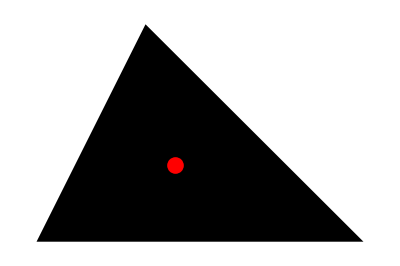

```mathematica
triangle={{-1,0},{2,0},{0,2}};
electroCenter=FindElectrostaticCenter2D[triangle];
Show[{
Graphics[Polygon[triangle]],
Graphics[{RGBColor[1,0,0],PointSize[.03],Point[electroCenter]}]
}]
```